RK4 Potencial Quadrado

```mathematica
ClearAll["Global`*"]
```

```mathematica
M=32;
m=2000;
ti=0.0;
tf=20π;
h=(tf-ti)/m;
```

Condição Inicial
-Graphics-

```mathematica
modo=3;
Do [
{X[i,1]=Sin[modo*π *i/(M+1)],
P[i,1]=0},
{i,1,M}
];
X[0,_]:=0;
X[M+1,_]:=0;
```

RK4

```mathematica
Do[
Do[

k1=h*P[i,n];
l1=h*(X[i+1,n]+X[i-1,n]-2*X[i,n]);

Xt2[i_]:=X[i,n]+k1/2;
Pt2[i_]:=P[i,n]+l1/2;
l2=h*(Xt2[i+1]+Xt2[i-1]-2*Xt2[i]);
k2=h*Pt2[i];

Xt3[i_]:=X[i,n]+k2/2;
Pt3[i_]:=P[i,n]+l2/2;
l3=h*(Xt3[i+1]+Xt3[i-1]-2*Xt3[i]);
k3=h*Pt3[i];

Xt4[i_]:=X[i,n]+k3;
Pt4[i_]:=P[i,n]+l3;
l4=h*(Xt4[i+1]+Xt4[i-1]-2*Xt4[i]);
k4=h*Pt4[i];

X[i,n+1]=X[i,n]+(1/6)*(k1+2*k2+2*k3+k4);
P[i,n+1]=P[i,n]+(1/6)*(l1+2*l2+2*l3+l4),

{i,1,M}],
{n,1,m}];
```

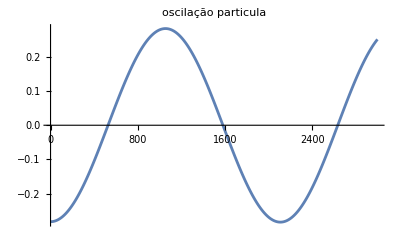

```mathematica
Clear[particula]
particula=12;
ListLinePlot[Table[X[particula,n],{n,1,m}],PlotRange->All,PlotLabel->"oscilação particula"]
```

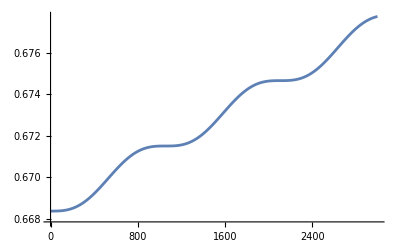

```mathematica
T[n_]:=Sum[1/2 P[i,n]^2,{i,1,M}];
V[n_]:=Sum[1/2 (X[i+1,n]-X[i,n])^2,{i,0,M}];
energia[n_]:=T[n]+V[n];
ListLinePlot[Table[energia[n],{n,1,m}],PlotRange->All]
```

```mathematica
frames=Table[ListPlot[Table[X[i,n],{i,1,M}],PlotRange->{{1,M},{-2,2}},PlotLabel->"Oscilação da cadeia Modo 3 "],{n,1,m,50}];

ListAnimate[frames]
```

```mathematica
Export["modo3.gif",%]
```

modo3.gif